Probability of the state actually being up or down

```mathematica
SpinUpProbability = 0.4;
SpinDownProbability = 0.6;
```

Some fake distributions (in place of randomised pulse durations and noise and filtering etc.)

```mathematica
SpinDownDist:=PDF[NormalDistribution[0.7,0.2]]
SpinUpDist:=PDF[NormalDistribution[2.5,0.35]][#]*80/100+PDF[NormalDistribution[1.8,0.45]][#]18/100+PDF[NormalDistribution[1,0.2]][#]2/100&
```

Check they look reasonabe (total integrals for up and down must each come to unity)

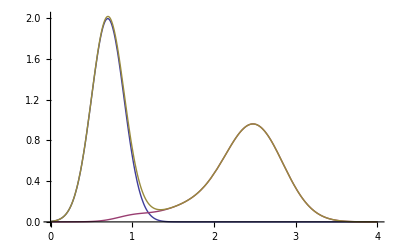

```mathematica
Plot[{SpinDownDist[pk],SpinUpDist[pk],SpinDownDist[pk]+SpinUpDist[pk]},{pk,0,4}]
```

Determine FIDELITY, the probability of measuring spin up given that it actually is a spin up state (same for down)

VISIBILITY is a combined measure of how good our threshold is for observing a state correctly

```mathematica
SpinUpFidelity:=1-Integrate[SpinUpDist[pk],{pk,-Infinity,#}]&
SpinDownFidelity:=1-Integrate[SpinDownDist[pk],{pk,#,Infinity}]&
SpinVisibility:=SpinDownFidelity[#]+SpinUpFidelity[#]-1&
```

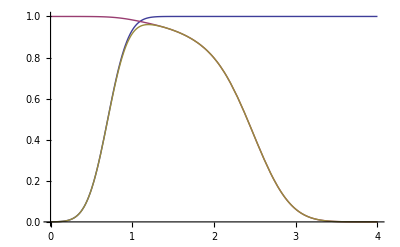

```mathematica
Plot[{SpinDownFidelity[th],SpinUpFidelity[th],SpinVisibility[th]},{th,0,4}]
```

All checks out ok, best visibility is at 1.2

```mathematica
Plot[{SpinDownFidelity[th],SpinUpFidelity[th],SpinDownFidelity[th]+SpinUpFidelity[th]-1},{th,1,1.4}]
```

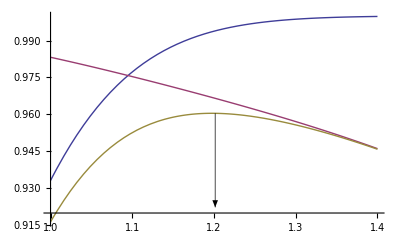

Determine CORRECTNESS, the probability that a state is/was actually spin up, given that it was measured as spin up (same for down)

INFERABILITY is a combined measure of how good the threshold is at correctly determining the true state based on the measurement outcome

MEASURABILITY turns out to be simply the probability of measuring a certain state, regardless of what it really is/was. It is needed for Bayes' law.

```mathematica
SpinUpMeasurability:= SpinUpFidelity[#]*SpinUpProbability+(1-SpinDownFidelity[#])*SpinDownProbability&
SpinDownMeasurability:= SpinDownFidelity[#]*SpinDownProbability+(1-SpinUpFidelity[#])*SpinUpProbability&
SpinUpCorrectness:=SpinUpFidelity[#]*SpinUpProbability/SpinUpMeasurability[#]&
SpinDownCorrectness:=SpinDownFidelity[#]*SpinDownProbability/SpinDownMeasurability[#]&
SpinInferability:=SpinUpCorrectness[#]+SpinDownCorrectness[#]-1&
```

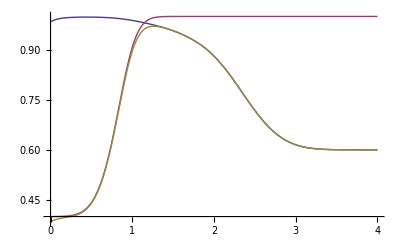

```mathematica
Plot[{SpinDownCorrectness[th],SpinUpCorrectness[th],SpinInferability[th]},{th,0,4}]
```

Blue curve goes down a bit near zero, assumed it would approach 1 - to do with artificially adding tail to spin up histogram. Ignore part below 0.2 on x-axis.

Best inferability is a bit above 1.2

```mathematica
Plot[{SpinDownCorrectness[th],SpinUpCorrectness[th],SpinInferability[th]},{th,1,1.4}]
```